```mathematica
20Log10[1/2]//N
10Log10[1/2]//N
```

-6.0206

-3.0103

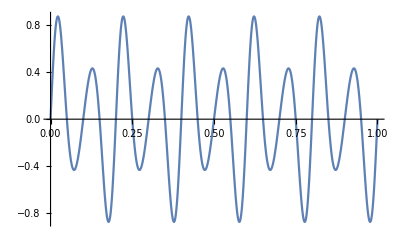

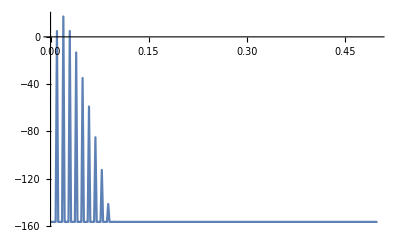

```mathematica
sr=512;tt=1/sr;
b=1;
fmod=5;
fc=10;
fsignal[n_]=Sin[2 Pi n fc] E^(-(b Sin[Pi fmod n])^2)//N;
Plot[fsignal[n],{n,0,1},PlotRange->All]
Periodogram[Table[fsignal[n],{n,0,1-tt,tt}]]
```